```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/ethans/GitHub/161/img

Ohm’s law.

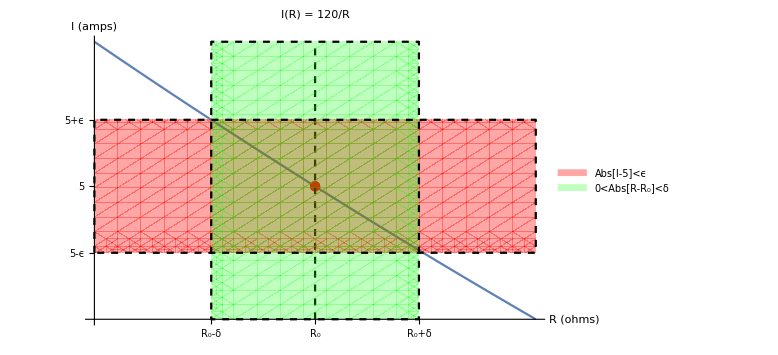

tol_reg.png

```mathematica
v0=120;
i0=5;
i[r_]=v0/r;
r0=r/.Solve[i[r]==i0,r][[1]];
{a,b}={r0-1,r0+1};
{c,d}={i[b],i[a]};
eps=1/10;
modelPlt=Plot[i[r],{r,a,b},AxesLabel->{ "R (ohms)","I (amps)"},PlotLabel->StringForm["I(R) = ``",i["R"]],ImageSize->Large];
target={r0,i0};
targetPnt=ListPlot[{target},PlotStyle->Red];
specLine=ContourPlot[r==r0,{r,a,b},{i,c,d},ContourStyle->{Black,Dashed}];
rInt=Reduce[Abs[i[r]-i0]<eps,r,Reals];
rmin=rInt[[1]];
rmax=rInt[[-1]];
del=Min[Abs[r0-rmin],Abs[r0-rmax]];
tolReg=RegionPlot[{Abs[i-i0]<eps,Abs[r-r0]<del},{r,a,b},{i,c,d},PlotStyle->{{Red,Opacity[0.35]},{Green,Opacity[0.25]}},BoundaryStyle->{{Black,Dashed}},PlotLegends->{Abs["I"-i0]<ϵ,0<Abs["R"-"R_0"]<δ}];
plt=Show[
modelPlt,
targetPnt,
specLine,
tolReg,
PlotRange->All,
Ticks->{{{r0-del,"R_0-δ"},{r0,"R_0"},{r0+del,"R_0+δ"}},{{i0-eps,"5-ϵ"},i0,{i0+eps,"5+ϵ"}}}
]
Export["tol_reg.png",plt]
```

Ideal gas law.

304.655

Target temperature is 31.51 degrees Celsius.

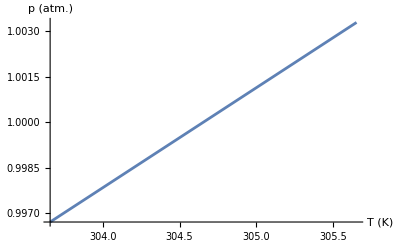

```mathematica
v0 = 100;(*liters*)
n = 4; (*moles of an ideal gas*)
r = 0.08206; (* (L.atm)/(mol.K) *)
p[t_] = n*r*t/v0;
p0 = 1; (* target pressure in atmospheres *)
t0 = t/.Solve[p[t]==p0,t][[1]]
StringForm["Target temperature is `` degrees Celsius.", NumberForm[t0-273.15,4]]
{a,b} = {t0-1, t0+1};
Plot[p[t],{t,a,b},AxesLabel->{"T (K)","p (atm.)"}]
```